```mathematica
currTime=0;
tStep=0.1;
ℏ=1;
ω=0.5;
m=1;
nMin=1;
nMax=10;
num=10;

(*when := you have a different definition*)
generateNthHarmonicOscillatorEigenstate[n_]:=1/(√(2^n n!))((m  ω)/(π ℏ))^(1/4)ⅇ^((-(m ω x^2))/(2 ℏ))HermiteH[n, √(m ω/ℏ)x];



(*Function to take in wavefunction and convert into a Wigner Function

to ask: is this valid syntax*)
WignerFunction[f_, t_]:=1/(π ℏ)Integrate[Conjugate[f[(x+y), t]]f[(x-y), t] ⅇ^(2 ⅈ p y/ℏ), {y, -∞, ∞},Assumptions->{x∈Reals, p∈Reals, t∈ Reals}]

hamonicOscEnergy[n_]:=ℏ ω(1/2+n);
calculateTimeFactor[n_, t_]:=ⅇ^(-ⅈ hamonicOscEnergy[n] t/ℏ)

generateNthHarmonicOscillatorEigenstateWithT[n_]:=1/(√(2^n n!))((m  ω)/(π ℏ))^(1/4)ⅇ^((-(m ω x^2))/(2 ℏ))HermiteH[n, √(m ω/ℏ)x]calculateTimeFactor[n, t];


A=1/(√2)
B=1/(√2)
C1=1/(√3)
D1=√(2/3)

Ψ1[x_, t_]=A*generateNthHarmonicOscillatorEigenstateWithT[1]+B*generateNthHarmonicOscillatorEigenstateWithT[2];

Ψ2[x_, t_]=C1*generateNthHarmonicOscillatorEigenstateWithT[3]+D1*generateNthHarmonicOscillatorEigenstateWithT[4];

ani=Animate[Plot[{Abs[Ψ1[x, t]]^2, Abs[Ψ2[x, t]]^2},{x,-10,10},PlotRange->{0,1}],{t,0,50}, AnimationRunning->False]
```

1/(√2)

1/(√2)

1/(√3)

√(2/3)

```mathematica
Export["anii.gif",ani]
```

anii.gif

```mathematica
Distances={};(*calculatethedistance*)
Distances=Table[{},{i, 0,50}]
```

```mathematica
ψ1[x_, t_]=generateNthHarmonicOscillatorEigenstateWithT[1]
ψ2[x_, t_]=generateNthHarmonicOscillatorEigenstateWithT[2]
W1[x_, p_,t_]=WignerFunction[ψ1, t]
W2[x_, p_,t_]=WignerFunction[ψ2, t]
```

0.631619 ⅇ^((0.-0.75 ⅈ) t-0.25 x^2) x

0.223311 ⅇ^((0.-1.25 ⅈ) t-0.25 x^2) (-2.+2. x^2)

(ⅇ^(-2. p^2-0.5 x^2) (-1.+4. p^2+1. x^2))/π

1/(π Abs[p])ⅇ^(-2. p^2-0.5 x^2) ((1.+8. p^4-2. x^2+0.5 x^4+p^2 (-8.+4. x^2)) Abs[p]+p ((0.-1.11022×10^-16 ⅈ)-(0.+5.55112×10^-17 ⅈ) x^2) Erfi[1.41421 Abs[p]])

```mathematica
ψ3[x_, t_]=generateNthHarmonicOscillatorEigenstateWithT[3]
W3[x_, p_,t_]=WignerFunction[ψ3, t]
```

0.0911663 ⅇ^((0.-1.75 ⅈ) t-0.25 x^2) (-8.48528 x+2.82843 x^3)

1/π ⅇ^(-2. p^2-0.5 x^2) (-1.+10.6667 p^6+3. x^2-1.5 x^4+0.166667 x^6+p^4 (-24.+8. x^2)+p^2 (12.-12. x^2+2. x^4)+2.36221×10^-16 ⅇ^(2. p^2) x^3 Hypergeometric1F1[1,1/2,-2. p^2])

```mathematica
Plot3D[W1[x, p, t],{x, -10,10},{p,-10,10},PlotRange->All]
Plot3D[W2[x, p, t],{x, -10,10},{p,-10,10},PlotRange->All]
Plot3D[W3[x, p, t],{x, -10,10},{p,-10,10},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
W[x_, p_, t_]=WignerFunction[ψ]
```

0.

0.

```mathematica
list2=Table[Plot3D[list[[i]],{x,-5,5},{p,-5,5},PlotRange->All],{i,1,Length[list]}]
```

```mathematica
ListAnimate[list2]
```

```mathematica
Export["quantum chaos animation.avi", list2]
```

quantum chaos animation.avi

```mathematica
Plot3D[z[x, p],{x, -5,5},{p,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
calculateEMD[finitnorm_, ffinalnorm_, xmin_, xmax_,ymin_, ymax_, nbox_, gridboxcutoff_]:=Module[{dx, dy, diffarray, outboxes, inboxes, nout, nin, nvars, mat0, supplyamount, demandamount, mat, distance, k, l, m, n, i, j},dx=(xmax-xmin)/nbox;dy=(ymax-ymin)/nbox;
f1[x_,p_]=finitnorm;
f2[x_,p_]=ffinalnorm;
diffarray=Table[Re[NIntegrate[Re[f1[x,p]-f2[x,p]],{x,xmin+(i-1)*dx,xmin+i*dx},{p,ymin+(j-1)*dy,ymin+j*dy}]],{i,1,nbox},{j,1,nbox}];

outboxes={};inboxes={}; 
For[i=1,i≤nbox,i++,
For[j=1,j≤nbox,j++,
If[diffarray[[i,j]]>gridboxcutoff,AppendTo[outboxes,{xmin+(i-.5)*dx,ymin+(j-.5)*dy}]];
If[diffarray[[i,j]]<-gridboxcutoff,AppendTo[inboxes,{xmin+(i-.5)*dx,ymin+(j-.5)*dy}]]]];
nout=Length[outboxes];nin=Length[inboxes];
nvars=nout*nin;
supplyamount ={}; demandamount = {};
For[i=1,i≤nbox,i++,
For[j=1,j≤nbox,j++,
If[diffarray[[i,j]]>gridboxcutoff,AppendTo[supplyamount,diffarray[[i,j]]]];
If[diffarray[[i,j]]<-gridboxcutoff,AppendTo[demandamount,diffarray[[i,j]]]];
]];
mat = Table[
EuclideanDistance[outboxes[[o]], inboxes[[q]]],{o,Length@outboxes},{q, Length@inboxes}];
mat0 = Table[0,{Length@outboxes+Length@inboxes},{Length@outboxes+Length@inboxes}];
For[i=1,i<=Length@outboxes,i++,
For[j=Length@outboxes+1,j≤(Length@inboxes+Length@outboxes),j++,
mat0[[i,j]]=mat[[i,j-Length@outboxes]]
]];

mat0//MatrixForm;

(*Then put in the numbers for the upper left section*)
For[k=1,k<=Length@outboxes,k++,
For[l=k+1,l≤Length@outboxes,l++,
mat0[[k,l]]=EuclideanDistance[outboxes[[k]], outboxes[[l]]]
]];

mat0//MatrixForm;
(*For the lower right..*)
For[m=Length@outboxes+1,m≤(Length@inboxes+Length@outboxes-1),m++,
For[n=m+1,n≤(Length@inboxes+Length@outboxes),n++,
mat0[[m,n]]=EuclideanDistance[inboxes[[m-Length@outboxes]], inboxes[[n-Length@outboxes]]]
]];

mat0//MatrixForm;
distance=FindMinimumCostFlow[ mat0, Join[supplyamount,demandamount]];
Print["Done one"];
Return[distance];
]
```

```mathematica
(*scale to nbox
divide by nbox square*)
```

```mathematica
Print["Done one"];
```

Done one

```mathematica
xmin=-5;xmax=5;ymin=-5;ymax=5;
nbox=40;
gridboxcutoff=.0001;
tstep=1;
tmax=20;
```

```mathematica
wignerFunctionsInit=Table[WignerFunction[Ψ1,t],{t,0,tmax,tstep}];
wignerFunctionsFin=Table[WignerFunction[Ψ2,t],{t,0,tmax,tstep}];
```

```mathematica
wignerFunctionsInit
```

{1/(π Abs[p])ⅇ^(-2. p^2-0.5 x^2) ((1.11022×10^-16+4. p^4-1.41421 x-(0.+2.22045×10^-16 ⅈ) ⅇ^(2. p^2) p x-0.5 x^2+0.707107 x^3+0.25 x^4+p^2 (-2.+2.82843 x+2. x^2)) Abs[p]+p ((0.-1.11022×10^-16 ⅈ)+p^2 ((0.+4.44089×10^-16 ⅈ)+(0.+2.22045×10^-16 ⅈ) x) x) Erfi[1.41421 Abs[p]]),1/π ⅇ^(-2. p^2-0.5 x^2) ((1.6626×10^-16-5.55964×10^-17 ⅈ)-(2.71204+8.88178×10^-16 ⅈ) p^3+(4.-4.44089×10^-16 ⅈ) p^4-(1.24109-1.66533×10^-16 ⅈ) x-(0.5-5.55112×10^-17 ⅈ) x^2+(0.620545-8.32667×10^-17 ⅈ) x^3+0.25 x^4+p ((1.35602+2.77556×10^-16 ⅈ)-(4.17018×10^-17+1.38564×10^-17 ⅈ) x-(0.67801+2.22045×10^-16 ⅈ) x^2)+p^2 ((-2.+1.11022×10^-16 ⅈ)+(2.48218-3.33067×10^-16 ⅈ) x+(2.-2.22045×10^-16 ⅈ) x^2)+(1.33093×10^-16+4.42232×10^-17 ⅈ) ⅇ^(2. p^2) p x Hypergeometric1F1[2,3/2,-2. p^2]),1/π ⅇ^(-2. p^2-0.5 x^2) ((1.61097×10^-16-9.84809×10^-17 ⅈ)-(4.76008+4.44089×10^-16 ⅈ) p^3+(4.+8.88178×10^-16 ⅈ) p^4-(0.764103+1.66533×10^-16 ⅈ) x-(0.5-2.77556×10^-17 ⅈ) x^2+(0.382051+1.38778×10^-16 ⅈ) x^3+(0.25+5.55112×10^-17 ⅈ) x^4+p ((2.38004+1.11022×10^-15 ⅈ)+(3.47858×10^-17-1.93418×10^-16 ⅈ) x-1.19002 x^2)+p^2 ((-2.+1.11022×10^-16 ⅈ)+(1.52821+5.55112×10^-16 ⅈ) x+(2.+4.44089×10^-16 ⅈ) x^2)+(1.69207×10^-16+4.7652×10^-16 ⅈ) ⅇ^(2. p^2) p Hypergeometric1F1[2,3/2,-2. p^2]),1/π ⅇ^(-2. p^2-0.5 x^2) ((3.32942×10^-16+1.09923×10^-16 ⅈ)-(5.64268+4.44089×10^-16 ⅈ) p^3+(4.-2.22045×10^-16 ⅈ) p^4-(0.100038+4.09395×10^-16 ⅈ) x-(0.5-2.77556×10^-17 ⅈ) x^2+(0.0500188+1.94289×10^-16 ⅈ) x^3+(0.25-4.16334×10^-17 ⅈ) x^4+p ((2.82134-6.66134×10^-16 ⅈ)-(1.41067+1.11022×10^-16 ⅈ) x^2)+p^2 ((-2.+1.11022×10^-16 ⅈ)+(0.200075+7.21645×10^-16 ⅈ) x+(2.-3.33067×10^-16 ⅈ) x^2)-(2.505×10^-17+3.59629×10^-17 ⅈ) ⅇ^(2. p^2) p x Hypergeometric1F1[2,3/2,-2. p^2]),1/π ⅇ^(-2. p^2-0.5 x^2) ((-5.14376-6.66134×10^-16 ⅈ) p^3+(4.+2.22045×10^-16 ⅈ) p^4+p ((2.57188+5.55112×10^-16 ⅈ)-(1.28594+1.66533×10^-16 ⅈ) x^2)+p^2 ((-2.-2.22045×10^-16 ⅈ)-(1.17704+1.11022×10^-16 ⅈ) x+(2.+1.11022×10^-16 ⅈ) x^2)+x ((0.588521+5.55112×10^-17 ⅈ)-0.5 x-(0.29426+2.77556×10^-17 ⅈ) x^2+(0.25+1.38778×10^-17 ⅈ) x^3)+(5.04325×10^-17-1.49186×10^-17 ⅈ) ⅇ^(2. p^2) p x Hypergeometric1F1[2,3/2,-2. p^2]),1/π ⅇ^(-2. p^2-0.5 x^2) ((2.80486×10^-16+4.92628×10^-18 ⅈ)-(3.38547+8.68905×10^-18 ⅈ) p^3+(4.-2.77556×10^-16 ⅈ) p^4+(1.13299-8.41533×10^-17 ⅈ) x-(0.5-2.63898×10^-17 ⅈ) x^2-(0.566494-6.42224×10^-17 ⅈ) x^3+(0.25-1.73472×10^-17 ⅈ) x^4+p ((1.69273+4.34452×10^-18 ⅈ)+(3.42131×10^-19-1.7586×10^-16 ⅈ) x-(0.846367+2.17226×10^-18 ⅈ) x^2)+p^2 ((-2.+1.27705×10^-16 ⅈ)-(2.26598-2.5689×10^-16 ⅈ) x+(2.-1.49851×10^-16 ⅈ) x^2)),1/π ⅇ^(-2. p^2-0.5 x^2) ((2.43074×10^-17-6.57761×10^-17 ⅈ)-(0.798295+8.88178×10^-16 ⅈ) p^3+(4.-2.22045×10^-16 ⅈ) p^4+(1.40006+1.11022×10^-16 ⅈ) x-(0.5+2.77556×10^-17 ⅈ) x^2-0.70003 x^3+(0.25-1.38778×10^-17 ⅈ) x^4+p ((0.399148+3.33067×10^-16 ⅈ)-(0.199574+1.52656×10^-16 ⅈ) x^2)+p^2 ((-2.+2.22045×10^-16 ⅈ)-(2.80012-1.11022×10^-16 ⅈ) x+2. x^2)+(3.26011×10^-16-4.77594×10^-16 ⅈ) ⅇ^(2. p^2) p x Hypergeometric1F1[2,3/2,-2. p^2]),1/π ⅇ^(-2. p^2-0.5 x^2) ((1.09512×10^-16+8.7616×10^-17 ⅈ)-(0.992165-1.11022×10^-16 ⅈ) p-(2.+3.33067×10^-16 ⅈ) p^2+(1.98433-3.33067×10^-16 ⅈ) p^3+(4.+4.44089×10^-16 ⅈ) p^4+(1.32435+3.33067×10^-16 ⅈ) x+(1.37211×10^-17+1.23531×10^-16 ⅈ) p x-2.6487 p^2 x-(0.5+1.38778×10^-16 ⅈ) x^2+(0.496082-5.55112×10^-17 ⅈ) p x^2+(2.+2.22045×10^-16 ⅈ) p^2 x^2-(0.662175+1.66533×10^-16 ⅈ) x^3+(0.25+2.77556×10^-17 ⅈ) x^4+ⅇ^(2. p^2) ((1.36848×10^-18+1.23205×10^-17 ⅈ)-(1.55021×10^-32+2.43229×10^-33 ⅈ) x+(5.476×10^-18-6.84448×10^-18 ⅈ) x^2) Hypergeometric1F1[1,1/2,-2. p^2]+ⅇ^(2. p^2) p ((-2.73696×10^-18-2.4641×10^-17 ⅈ)+(3.70834×10^-32+9.72825×10^-33 ⅈ) x^2+(1.09478×10^-17+9.85638×10^-17 ⅈ) x^3-(1.0952×10^-17-1.3689×10^-17 ⅈ) x^4) Hypergeometric1F1[1,3/2,-2. p^2]-(1.3689×10^-17+1.0952×10^-17 ⅈ) ⅇ^(2. p^2) Hypergeometric1F1[2,1/2,-2. p^2]+(4.37914×10^-17+3.94255×10^-16 ⅈ) ⅇ^(2. p^2) p Hypergeometric1F1[2,3/2,-2. p^2]+(1.75232×10^-16-2.19023×10^-16 ⅈ) ⅇ^(2. p^2) p x Hypergeometric1F1[2,3/2,-2. p^2]+(5.47558×10^-17+4.3808×10^-17 ⅈ) ⅇ^(2. p^2) p x^2 Hypergeometric1F1[2,3/2,-2. p^2]-(1.97128×10^-16-2.18957×10^-17 ⅈ) ⅇ^(2. p^2) p Hypergeometric1F1[3,3/2,-2. p^2]),1/π ⅇ^(-2. p^2-0.5 x^2) ((-7.95289×10^-17+1.35136×10^-16 ⅈ)+(4.28112-7.08664×10^-16 ⅈ) p^3+4. p^4+0.924392 x-0.5 x^2-0.462196 x^3+0.25 x^4+p ((-2.14056+1.77166×10^-16 ⅈ)-(5.18623×10^-17-2.43112×10^-16 ⅈ) x+(1.07028-8.8583×10^-17 ⅈ) x^2)+p^2 ((-2.+1.77166×10^-16 ⅈ)-1.84878 x+2. x^2)),1/π ⅇ^(-2. p^2-0.5 x^2) ((1.62207×10^-16+6.65007×10^-17 ⅈ)+(5.52975+1.77166×10^-16 ⅈ) p^3+4. p^4+(0.29811+1.32874×10^-16 ⅈ) x-(0.5+2.21457×10^-17 ⅈ) x^2-(0.149055+4.98279×10^-17 ⅈ) x^3+(0.25+1.10729×10^-17 ⅈ) x^4+p ((-2.76487+3.54332×10^-16 ⅈ)+(1.38244+4.42915×10^-17 ⅈ) x^2)+p^2 ((-2.-3.54332×10^-16 ⅈ)-(0.596221+1.99312×10^-16 ⅈ) x+(2.+8.8583×10^-17 ⅈ) x^2)),1/π ⅇ^(-2. p^2-0.5 x^2) ((1.38776×10^-16+2.67938×10^-17 ⅈ)+(5.42449-2.2584×10^-16 ⅈ) p^3+(4.-1.66533×10^-16 ⅈ) p^4-(0.401159-1.05285×10^-16 ⅈ) x-(0.5-4.20737×10^-18 ⅈ) x^2+(0.200579-5.26423×10^-17 ⅈ) x^3+(0.25-1.31766×10^-17 ⅈ) x^4+p ((-2.71225-1.99545×10^-17 ⅈ)-(5.48085×10^-17+3.64303×10^-18 ⅈ) x+(1.35612+2.10501×10^-17 ⅈ) x^2)+p^2 ((-2.-1.16045×10^-16 ⅈ)+(0.802318-2.10569×10^-16 ⅈ) x+(2.-1.05412×10^-16 ⅈ) x^2))}

```mathematica
distances=Table[calculateEMD[wignerFunctionsInit[[i]], wignerFunctionsFin[[i]], xmin, xmax,ymin, ymax, nbox, gridboxcutoff],{i,1,Length[wignerFunctionsInit]}]
```

Done one

Done one

Done one

«8 more identical outputs»

{1.13455,1.12547,1.10924,1.0969,1.10477,1.12136,1.13383,1.13011,1.11472,1.09856,1.10009}

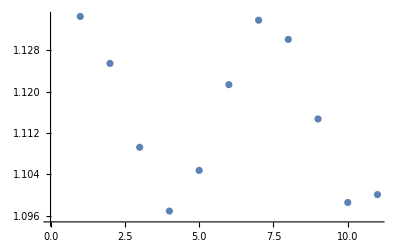

```mathematica
ListPlot[distances]
```

```mathematica
re=calculateEMD[wignerFunctionsInit[[1]], wignerFunctionsFin[[1]], xmin, xmax,ymin, ymax, nbox, gridboxcutoff]
```

Done one

1.13455

```mathematica
Re[wignerFunctionsInit[[1]]]
```

1/π Re[1/Abs[p]ⅇ^(-2. p^2-0.5 x^2) ((1.11022×10^-16+4. p^4-1.41421 x-(0.+2.22045×10^-16 ⅈ) ⅇ^(2. p^2) p x-0.5 x^2+0.707107 x^3+0.25 x^4+p^2 (-2.+2.82843 x+2. x^2)) Abs[p]+p ((0.-1.11022×10^-16 ⅈ)+p^2 ((0.+4.44089×10^-16 ⅈ)+(0.+2.22045×10^-16 ⅈ) x) x) Erfi[1.41421 Abs[p]])]

```mathematica
FullSimplify[(2x^2-x+3x^3)/((1-x^2)^2)]
```

(x (-1+3 x))/((-1+x)^2 (1+x))

```mathematica
Factor[1-x-x^2]
```

1-x-x^2

```mathematica
FullSimplify[(2 x^2)/((1-x^2)^2)+x((2 x^2)/((1-x^2)^2)-1/(1-x^2))]
```

(x (-1+3 x))/((-1+x)^2 (1+x))

```mathematica
Expand[x^2(1+x^2)/((1-x^2)^2)]
```

x^2/((1-x^2)^2)+x^4/((1-x^2)^2)

PolynomialQuotient::argr: PolynomialQuotient called with 1 argument; 3 arguments are expected.

PolynomialQuotient[(x^2 (1+x^2))/((1-x^2)^2)]